```mathematica
Get[NotebookDirectory[]<>#]&/@
{"load_takahashi_data.wl",
"styles.wl"
};
```

## Fit temperature deactivation

```mathematica
(*from no-stress parameters*)
fit0={αU->6.249999999999999*^8,αPtotalP->1.1607142857142856*^9};
(*data on FvFm from Takahashi*)
FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]];
```

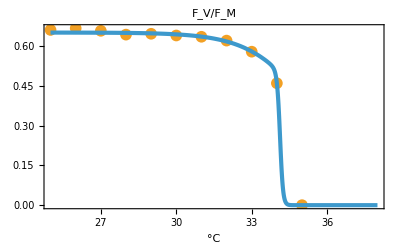

{σT1→75880.5,σT2→1.62172×10^6,ρT→0.001,γT1→0.00175396,γT2→11270.4,wRef→35.}

```mathematica
(*αP without damage, at given temperature*)
αPxxx=αPtotalP ρT/(ρT+γT1  ⅇ^(-σT1/(w+273))/ⅇ^(-σT1/(wRef+273))+γT2  ⅇ^(-σT2/(w+273))/ⅇ^(-σT2/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit0,ρT==10^-3,wRef==35,σT1>0,(*1.4 10^6>*)σT2>0,γT1>0,γT2>0},{{σT1,10^5},{σT2,10^6},{ρT,10^-3},{γT1,10^-3},{γT2,10^4},{wRef,35}},w];
(Export[NotebookDirectory[]<>"export/direct-temperature-effect/two-step-arrhenius.pdf",#];#)&@Row[{
Show[
ListPlot[FvFmDarkData,
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
Plot[FvFmTempFit[W],{W,25,38},Evaluate@style,PlotStyle->{{colorCurves,thickness}}],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
FvFmTempFit["BestFitParameters"]
```

## Alternative: single Arrhenius

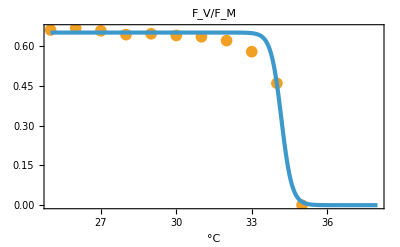

{σT→452022.,γT→0.143918,ρT→0.001,wRef→35.}

```mathematica
αPxxx=αPtotalP ρT/(ρT+γT  ⅇ^(-σT/(w+273))/ⅇ^(-σT/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]];
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit0,ρT==10^-3,wRef==35,(*1.4*)(*3 10^5>*)σT>0(*5 10^5*),γT>0},{{σT,1},{γT,.01},{ρT,10^-3},{wRef,35}},w];
(Export[NotebookDirectory[]<>"export/direct-temperature-effect/single-step-arrhenius-alternative.pdf",#];#)&@Row[{
Show[
ListPlot[FvFmDarkData,
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
Plot[FvFmTempFit[W],{W,25,38},Evaluate@style,PlotStyle->{{colorCurves,thickness}}],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
FvFmTempFit["BestFitParameters"]
```